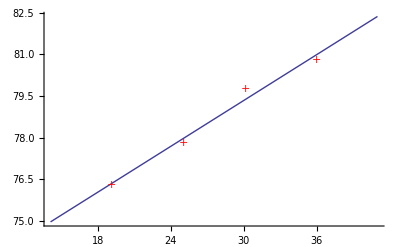

Значение сопротивления в точке t=30 равно: 79.3386

```mathematica
(*Зададим значения температуры*)
T={19.1,25.0,30.1,36.0};
(*Зададим значение сопротивления*)R={76.30,77.80,79.75,80.80};
(*Найдем количество уравнений системы*)
m=Dimensions[T][[1]];
(*Зададим количество параметров уравнения*)
n=2;
(*Зададим параметры уравнения*)
A=Array[a,n];
(*Зададим зависимость между температурой и сопротивлением*)
r[t_]=A.{1,t};
(*Построим сумму квадратов отклонений левых частей системы уравнений от правых*)
S=Sum[(r[T[[i]]]-R[[i]])^2,{i,1,m}];
(*Найдем минимум функции S*)
M=Minimize[S,A];
(*Найдем коэффициенты искомой зависимости*)k=Table[a[j]/.M[[2,j]],{j,1,n}];
(*Зададим найденную зависимость*)
sol[t_]=k.{1,t};
(*Построим экспериментальные точки и найденную зависимость в одчной системе координат*)
Experiment=Table[{T[[i]],R[[i]]},{i,1,m}];
GEx=ListPlot[Experiment,PlotStyle->Red,PlotMarkers->"+"];
G=Plot[sol[t],{t,T[[1]]-5,T[[m]]+5}];
Show[G,GEx]
tpoint=30;
Print["Значение сопротивления в точке t=",tpoint," равно: ",sol[tpoint]]
```